```mathematica
(*Equations A.6 and A.7, variation on n=2*)
Clear[mh,dmh,mw]
mh:=√2
dmh:=2(*2.966*mh*)(*sqrt8.8 as in email*)
mw:=mh/2

sol = NDSolve[{a''[r] -(mh^2+dmh^2)*a[r]+(b[r])^2/(4*r)== 0,b''[r]-mw^2*b[r]-(2*b[r])/r^2+mw^2/r*a[r]*b[r]==0,a[4]==6.1,a[0.2]==7.2,b[4]==5.5,b[0.2]==0.8},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[4]==6.1,b[4]==5.5,a'[4]==5.2,b'[4]==-0.9}},MaxSteps->10000];
```

NDSolve::ndsz: At r == 0.971679, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.16242, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 0.296745, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: "ndsz" will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: There are significant errors {-1.24632, -0.122589, 0.808345, -0.0171706} in the boundary value residuals.  Returning the best solution found.

InterpolatingFunction::dmval: Input value {0.10008} lies outside the range of data in the interpolating function. Extrapolation will be used.

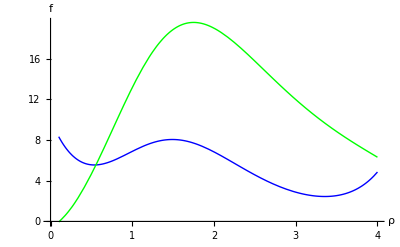

```mathematica
Plot[{Evaluate[a[r] /. sol],Evaluate[b[r] /. sol]}, {r,0.1,4},PlotStyle->{Blue,Green},AxesLabel->{ρ,f},AxesOrigin->{0,0}]
(*a/r is blue   b/r is green*)
```

```mathematica
(*Archive

a[7.1]==2.1,a[0.4]==27.8,b[0.4]==-1.6,b[7.1]==6.4},{a,b},r, Method->{"Shooting","StartingInitialConditions"->{a[7.1]==2.1,b[7.1]==6.4,a'[7.1]==-0.1,b'[7.1]==-0.3}}];*)
```

```mathematica
(*potential break for dmh = 8.8  r == 6.176203410610227 at BC for standard n=2*)
(*  r == 6.112769388798094 for a[8.0]==1.1,a[1.0]==5.2,b[8.0]==2.3,b[1]==-7.5, a'[8.0]==-0.2 b'[8.0]==-0.5*)
(* if i start at 6.0 then r ==4.14*)

(*2.25
```